# My ...project.

### Double-Slit configuration

```mathematica
d=(5 104.1)/10^6;(*meter*)
a1=21.9*10^-6;(*left slit in meter*) 
a2=22.5*10^-6;(*right slit in meter*)
x1=-(a1+d)/2;(*the center of left slit*)
x2=(a2+d)/2;(*the center of right slit*)
σ=2(a1+a2);
τ=d/(ℏ/((a1+a2)/2)/m);(*the time that it takes two Gaussian along x-axis meet each other*)
pz=.0001 √((h/λdB)^2-(ℏ/a1)^2);(*momentum along z-direction*)
```

### Physical Constants

```mathematica
c=QuantityMagnitude@UnitConvert[Quantity["SpeedOfLight"]];
eV=QuantityMagnitude@UnitConvert[Quantity["Electronvolts"]];
h=QuantityMagnitude@UnitConvert[Quantity["PlanckConstant"]];
ℏ=QuantityMagnitude@UnitConvert[Quantity["ReducedPlanckConstant"]];
m=QuantityMagnitude@UnitConvert[Quantity["NeutronMass"]];
λdB=h/(m*214.4);
```

### adfssdafj

```mathematica
ψ[p_][x0_,x_][t_]:=(1/(2π σ^2))^(1/4)Exp[ⅈ/ℏ p x -(x-x0-(p t)/m )^2/(4 σ^2)];
ϕ[x_,t_]:=(ψ[ℏ/a1][x1,x][t]+ψ[-ℏ/a2][x2,x][t])/√2;
Manipulate[Plot[{Abs[#]^2&@ψ[ℏ/a1][x1,x][t],Abs[#]^2&@ψ[-ℏ/a2][x2,x][t],Abs[#]^2&@ϕ[x,t]},{x,-d,d},Frame->True,PlotRange->{All,{0,10000}},Filling->Automatic,PlotStyle->{{Red,Dashed},{Green,Dashed},{Black,Thick}},FrameTicks->{Automatic,None}],{t,0,τ}]
```

Plot::plln: Limiting value -d in {x,-d,d} is not a machine-sized real number.

```mathematica
ListAnimate@Table[Plot3D[Abs[ϕ[x,t] ψ[pz][0,z][t]]^2,{x,-d,d},{z,-d,8 d},PlotPoints->30,PlotRange->{0,10^6},Ticks->{All,All,All},Mesh->False],{t,0,τ,τ/10}]
```

```mathematica
Manipulate[Plot3D[Abs[(ϕ[x,t])ψ[pz][0,z][t]]^2,{x,-d,d},{z,-d,8d},PlotRange->All,Ticks->{All,All,None},Mesh->False],{t,0,τ}]
```

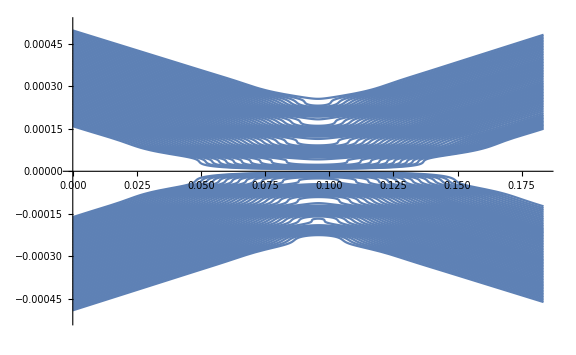

```mathematica
bohmTrajectory[q0_,tf_]:=Module[{ϕ,guidingDE,nde},
ϕ[x_,t_]:=ψ[ℏ/a1][x1,x][t]+ψ[-ℏ/a2][x2,x][t];
guidingDE=q'[t]==ℏ/m Im[Conjugate[ϕ[q[t],t]] D[ϕ[q[t],t],q[t]]]/(ϕ[q[t],t]Conjugate[ϕ[q[t],t]]);
nde=NDSolve[{guidingDE,q[0]==q0},q,{t,0,tf}];
Plot[Evaluate[q[t]/.nde],{t,0,tf},PlotRange->{All,{-d,d}},ImageSize->Large]]
Show[Table[bohmTrajectory[x2-5a2+i a2/4,τ],{i,0,60}],Table[bohmTrajectory[x1+5a1-i a1/4,τ],{i,0,60}]]
```

```mathematica
conjψ[p_][x0_,x_][t_]:=(1/(2π σ^2))^(1/4)Exp[-ⅈ/ℏ p x -(x-x0-(p t)/m )^2/(4 σ^2)];
```

```mathematica
conjϕ[x_,t_]:=(conjψ[ℏ/a1][x1,x][t]+conjψ[-ℏ/a2][x2,x][t])/√2;
```

```mathematica
ρ[x_,t_]:=conjϕ[x,t] ϕ[x,t];
```

Here is the scaled quantum potential:

```mathematica
qQ[q_,t_]:=N[(-ℏ^2/(4m))/(10^-13 eV)((Derivative[2,0][ρ][q,t])/ρ[q,t]-1/2((Derivative[1,0][ρ][q,t])/ρ[q,t])^2)]//Re;
```

```mathematica
Remove[qQ2]
```

```mathematica
qQ2[q_,t_]=(-ℏ^2/(4m))/(10^-13 eV)((Derivative[2,0][ρ][q,t])/ρ[q,t]-1/2((Derivative[1,0][ρ][q,t])/ρ[q,t])^2);
```

```mathematica
Manipulate[Plot[qQ2[q,t],{q,0,d/5},PlotRange->{-3,1}],{t,0,τ/2+τ/5}]
```

```mathematica
Manipulate[Plot[qQ[q,t],{q,-d/2,d/2}],{t,0,τ/2+τ/5}]
```

```mathematica
Manipulate[Plot[qQ[q,t]/.t->tf,{q,-d/2,d/2}],{tf,0,τ/2+τ/5}]
```

```mathematica
Plot3D[qQ2[q,t],{q,-d/2,d/2},{t,τ/2-τ/5,τ/2+τ/5},PlotPoints->50,MaxRecursion->3,Mesh->None]
```

-Graphics3D-

```mathematica
f[x_,t_]:=Derivative[1,0][g][x,t];
f[2,0]
```

g^(1,0)[2,0]

```mathematica
Derivative[1,0][g][2,0]
```

g^(1,0)[2,0]